```mathematica
pxy = c(k^2 + l^2)
Solve[Sum[Sum[pxy, {k, {-1, 0, 1, 3}}], {l, {-1, 2, 3}}] == 1, c]
```

c (k^2+l^2)

{{c→1/89}}

Piecewise[{{24 x y, 0<x<1&&0<y<1&&x+y<1}, {0, True}}]

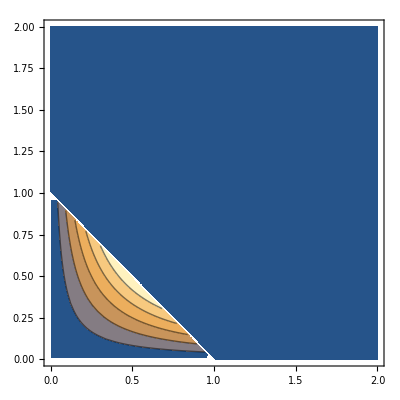

```mathematica
pxy = Piecewise[{{24 x y, 0 < x < 1 && 0 <y < 1&& x + y < 1}, {0, True}}]
ContourPlot[pxy, {x, 0, 2}, {y, 0, 2}]
```

```mathematica
Show[%72,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
Show[%73,ViewPoint->Front]
```

-Graphics3D-

```mathematica
Show[%74,ViewPoint->{0,0,∞}]
```

-Graphics3D-

```mathematica
Show[%75,ViewPoint->Above]
```

-Graphics3D-

```mathematica
Show[%76,ViewPoint->Below]
```

-Graphics3D-

```mathematica
Show[%77,ViewPoint->Back]
```

-Graphics3D-

```mathematica
Show[%78,ViewPoint->Left]
```

-Graphics3D-

```mathematica
Show[%79,ViewPoint->Right]
```

-Graphics3D-

```mathematica
Show[%80,ViewPoint->{0,0,∞}]
```

-Graphics3D-

```mathematica
Show[%81,ViewPoint->{0,0,-∞}]
```

-Graphics3D-

```mathematica
Show[%82,ViewPoint->{0,-∞,0}]
```

-Graphics3D-

```mathematica
Show[%83,ViewPoint->{-∞,0,0}]
```

-Graphics3D-

```mathematica
Show[%84,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
∫_(-∞)^∞ ∫_(-∞)^((1/2)-x) pxy ⅆy ⅆx
```

1/16

```mathematica
pxy = Piecewise[{{1 - Exp[-x^2]-Exp[-y^2]+Exp[-x - y], x≥0 && y ≥0}, {0, True}}]
```

Piecewise[{{1-ⅇ^(-x^2)+ⅇ^(-x-y)-ⅇ^(-y^2), x≥0&&y≥0}, {0, True}}]

```mathematica
D[D[pxy, x], y]
```

Piecewise[{{2 ⅇ^(-x^2) x-ⅇ^(-x-x^2-y) (-ⅇ^(x^2)+2 ⅇ^(x+y) x), x≥0&&y≥0}, {0, True}}]

```mathematica
Simplify[Piecewise[{{2 ⅇ^(-x^2) x-ⅇ^(-x-x^2-y) (-ⅇ^(x^2)+2 ⅇ^(x+y) x),x≥0&&y≥0}},0]]
```

Piecewise[{{ⅇ^(-x-y), x≥0&&y≥0}, {0, True}}]

```mathematica
Plot3D[Piecewise[{{ⅇ^(-x-y),x≥0&&y≥0}},0],{x,-5.895879734614027,5.895879734614027},{y,-5.895879734614027,5.895879734614027}]
```

-Graphics3D-

```mathematica
Plot3D[Piecewise[{{2 ⅇ^(-x^2) x-ⅇ^(-x-x^2-y) (-ⅇ^(x^2)+2 ⅇ^(x+y) x),x≥0&&y≥0}},0],{x,-1.4788994051326179,1.4788994051326179},{y,-4.527839646152036,4.527839646152036}]
```

-Graphics3D-

```mathematica
pxy = Piecewise[{{24 y (1-x-y), x > 0 && y > 0 && x+ y < 1}, {0, True}}]
```

Piecewise[{{24 (1-x-y) y, x>0&&y>0&&x+y<1}, {0, True}}]

```mathematica
mx =∫_(-∞)^∞ pxy ⅆx
```

Piecewise[{{12 (y-2 y^2+y^3), 0<y<1}, {0, True}}]

```mathematica
my =∫_(-∞)^∞ pxy ⅆy
```

Piecewise[{{-4 (-1+x)^3, 0<x<1}, {0, True}}]

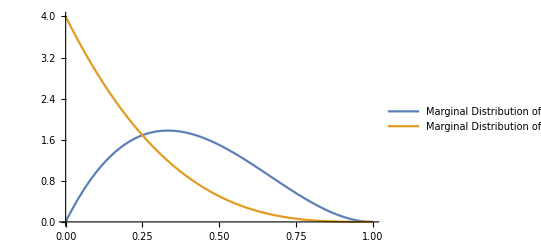

```mathematica
Plot[{
mx, 
my/.{x->y}}, 
{y, 0, 1}, 
PlotLegends->{"Marginal Distribution of y", "Marginal Distribution of x"}]
```

```mathematica
ProbabilityDistribution[2(1/3)^k,{k,1,∞}]
```

ProbabilityDistribution[2 3^-x,{x,1,∞}]

```mathematica
MomentGeneratingFunction[ProbabilityDistribution[2 3^-x,{x,1,∞}],t]
```

-(2 ⅇ^t)/(3 t-Log[27])

```mathematica
firstMoment = D[(-(2 ⅇ^t)/(3 t-Log[27])), t]
```

(6 ⅇ^t)/(3 t-Log[27])^2-(2 ⅇ^t)/(3 t-Log[27])

```mathematica
secondMoment = D[((6 ⅇ^t)/(3 t-Log[27])^2-(2 ⅇ^t)/(3 t-Log[27])), t]
```

-(36 ⅇ^t)/(3 t-Log[27])^3+(12 ⅇ^t)/(3 t-Log[27])^2-(2 ⅇ^t)/(3 t-Log[27])